```mathematica
n=50;
```

```mathematica
(*k=AdjacencyMatrix[RandomGraph[{n,100}]];
AdjacencyGraph[k]*)
```

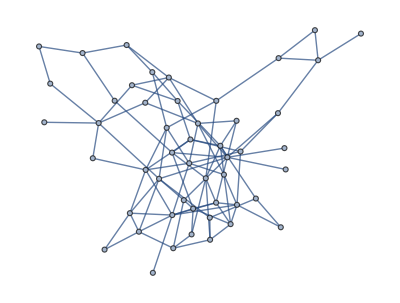
```mathematica
k1=-Graphics-;
```

```mathematica
k=AdjacencyMatrix[k1]
```

SparseArray[<200>, {50, 50}]

```mathematica
data={-2.4414919529410586,-0.5261830395652305,0.7033555402305138,2.0423094765020453,-2.040947937919583,-2.310561909793679,-0.10936600528287044,2.9273613224924864,-0.6438584422669952,-1.4273859005840372,-2.560973503119267,-0.1646128494442843,-0.9074922228420206,0.45119332562032666,-1.282661840204519,0.6512257765161864,0.4278615595196758,-0.9950121046200134,-2.693711562178278,0.4658656482963177,2.8031390145512085,-2.4661050712755506,0.665632810092718,-0.1974602815449598,-0.7802648047129704,-3.047670567230124,2.831684890621464,0.8388264491549847,3.0099758024606613,-0.38772046237313706,1.1054655745368578,-1.7692643776449704,-2.832951892103078,-3.031407135051544,2.404245462343435,2.2779203039335383,1.3604264915903028,1.3464475604303232,-1.8812400014644075,1.703293716142256,0.9139547111707235,-2.489057097848757,1.3940021590983596,-0.029443411455853847,-0.19218150732052625,-2.6644504708233825,-1.9849716206383554,-2.277243738710905,-0.30584224348614736,1.7966694175113254};
```

```mathematica
m=3;
(*data=RandomVariate[VonMisesDistribution[0,0],n];*)
cmsol=Solve[1+a Sum[(m+1-mm)Cos[(2mm Pi)/(m+1)],{mm,1,m}]==0,a];
cmkoef=a/.cmsol[[1]];
eqns=Table[{Subscript[∅,i]'[t]==4.5-3.5/n Sum[k[[i]][[j]](cmkoef Sum[mm(m+1-mm)Sin[mm(Subscript[∅,j][t]-Subscript[∅,i][t])],{mm,1,m}]),{j,1,n}],Subscript[∅,i][0]==data[[i]]},{i,1,n}];
vars=Table[Subscript[∅,i][t],{i,1,n}];
sol=NDSolve[eqns,vars,{t,0,10000}];
Do[Subscript[z,i][t_]:=Evaluate[Subscript[∅,i][t]/.sol],{i,1,n}];
Do[Subscript[zz,i][t_]:=Evaluate[ⅇ^(ⅈ×Subscript[∅,i][t]/.sol)],{i,1,n}];
data1[t_]:=Flatten[Table[Subscript[zz,i][t],{i,1,n}]];
tt=10000;
lista=Sort[Table[Mod[Subscript[z,i][tt],2Pi][[1]],{i,1,n}]];
lisboj[t_]:=Table[Mod[Subscript[z,i][t],2Pi][[1]],{i,1,n}];
SomeGraph=AdjacencyGraph[k];
Table[lista[[i]]-lista[[i+1]],{i,1,n-1}]
ukupfrust[t_]:=Sum[k[[i]][[j]](1+cmkoef Sum[(m+1-mm)Cos[mm(Subscript[z,j][t]-Subscript[z,i][t])],{mm,1,m}]),{i,1,n},{j,i+1,n}]
ukupfrust[5000]
data2=Flatten[Table[Mod[Subscript[z,i][tt],2Pi],{i,1,n}]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-7.27596×10^-12,-1.5708,0.,0.,0.,0.,0.,0.,0.,0.,0.,-7.27596×10^-12,0.,0.,-1.5708,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.5708,-7.27596×10^-12,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.}

{5.42378,5.42378,0.71139,2.28219,3.85298,2.28219,5.42378,2.28219,5.42378,3.85298,3.85298,0.71139,5.42378,2.28219,3.85298,0.71139,0.71139,5.42378,3.85298,0.71139,3.85298,3.85298,2.28219,0.71139,3.85298,3.85298,2.28219,0.71139,2.28219,5.42378,0.71139,3.85298,2.28219,2.28219,0.71139,2.28219,2.28219,0.71139,5.42378,2.28219,5.42378,0.71139,2.28219,5.42378,5.42378,3.85298,5.42378,3.85298,5.42378,0.71139}

```mathematica
zvuk={4,4,1,2,3,2,4,2,4,3,3,1,4,2,3,1,1,4,3,1,3,3,2,1,3,3,2,1,2,4,1,3,2,2,1,2,2,1,4,2,4,1,2,4,4,3,4,3,4,1};
```

```mathematica
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];
Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];
findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

```mathematica
a=Table[findAllRoots[Sin[(Subscript[z,i][t])/2],{t,0,60}],{i,1,n}];
```

```mathematica
Sound[Flatten[Table[Table[If[Round[a[[i]][[j]],0.05]==t,If[zvuk[[i]]==1,SoundNote["G",{60-t,60-t+0.1},"Oboe"],If[zvuk[[i]]==2,SoundNote["B",{60-t,60-t+0.1},"Oboe"],If[zvuk[[i]]==3,SoundNote["D",{60-t,60-t+0.1},"Oboe"],SoundNote["F",{60-t,60-t+0.1},"Oboe"]]]],SoundNote[None,{60-t,60-t+0.1}]],{i,1,n},{j,1,Length[a[[i]]]}],{t,60,0,-0.05}]],{0,80.066}]
```

```mathematica
Export["sim10_oboe.mp3",%33]
```

sim10_oboe.mp3

```mathematica
Export["MIDI_SM12.mid",%33]
```

MIDI_SM12.mid

```mathematica
granica=60;
```

```mathematica
video[t_]:=Grid[{{GraphPlot[SomeGraph,PlotStyle->{Gray,Thickness[0.004]},VertexRenderingFunction->({Hue[Rescale[lisboj[60-t][[Sequence@@#2]],{0,2Pi}]],Disk[#1,0.12]}&),ImageSize->700,PlotRangePadding->0],Show[{With[{sectors=360},angle=2 Pi/sectors;
Graphics[{Table[{Hue[i/sectors],EdgeForm[{Thick,Hue[i/sectors]}],Disk[{0,0},1,{i angle,(i+1) angle}]},{i,0,sectors-1}]}]],ListPlot[{Re[#],Im[#]}&/@data1[60-t],PlotStyle->Directive[Black,PointSize[.025]]],ListPlot[{0,1},PlotStyle->Directive[Gray,PointSize[.025]]]},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,25],Axes->True,AxesOrigin->{0,0},PlotRange->{{-1.1,1.1},{-1.1,1.1}},ImagePadding->40,AspectRatio->1],Show[{Plot[ukupfrust[60-tt],{tt,0,t+0.0000000001},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},PlotStyle->Directive[If[Chop[ukupfrust[10000]][[1]]==0,Red,Blue],Thickness[0.01]]]},AxesOrigin->{0,0},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},ImageSize->600,Frame->True,FrameStyle->Directive[Black,25]]}},Spacings->0]
```

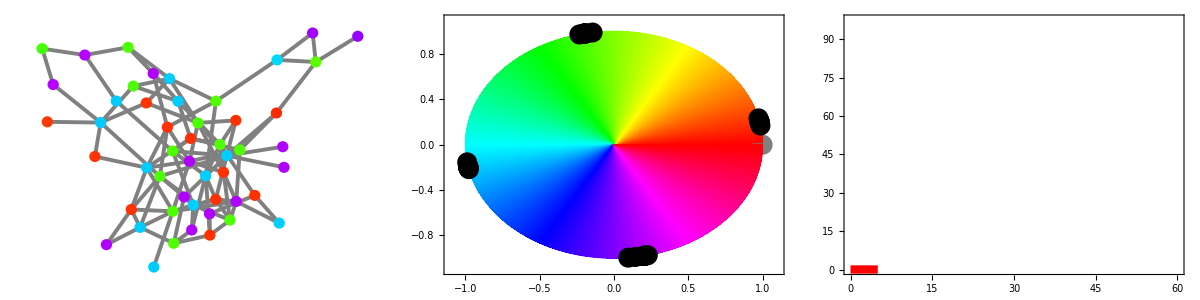

```mathematica
video[5]
```

```mathematica
simulaci1=Table[video[t],{t,0,60,0.05}];
```

```mathematica
Export["SM12.AVI",simulaci1]
```